```mathematica
"
```

```mathematica
Directory[]
```

/home/rui/prc2/simulaciones/sim_2do_cuatri/pruebas-rui/plots

```mathematica
lts
```

```mathematica
FilePrint["r_out.txt"]
```

```mathematica
vo1G=SemanticImport[ "r_out_rl=1g.txt"][All, {2->parseComplexLTSpice}];//Quiet
```

```mathematica
vo2=SemanticImport[ "r_out_rl=2.txt"][All, {2->parseComplexLTSpice}];//Quiet
```

```mathematica
vo1Gts=ro1G[All, Values][TimeSeries];
vo2ts=ro2[All, Values][TimeSeries];
```

v_o=R_L/(R_L+r_o)v_T

```mathematica
Solve[{vout1==rl1/(rl1+ro)vt , vout2==rl2/(rl2+ro)vt}, ro, Reals]
```

{}

```mathematica
Block[{rl1, rl2, vout1, vout2},
ro[vout1_, vout2_]=(rl1 rl2 (vout1-vout2))/(-rl2 vout1+rl1 vout2)/.{rl1->2, rl2->1*^9};
]
```

```mathematica
SetAttributes[ro, Listable];
```

```mathematica
TimeSeriesMapThread[ro, {vo2ts,vo1Gts}]//Head
```

List

```mathematica
vo2ts
```

```mathematica
ro[vo1Gts+vo2ts]
```

ro[TimeSeries[…]]

```mathematica
r=TimeSeriesThread[ro@*Apply[Sequence], {vo2ts,vo1Gts}];
```

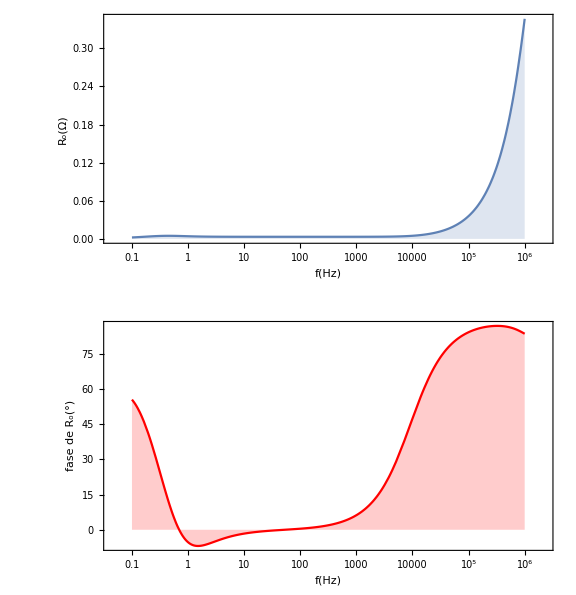

```mathematica
gr=GraphicsColumn[{
LogLinearPlot[Abs@r[f], {f, 0.1, 1000000},Filling->0,PlotRange->{0, Full},PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,0}}, FrameLabel->{"f(Hz)","R_o(Ω)"}, AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}],
LogLinearPlot[(Arg@r[f])/Degree, {f, 0.1, 1000000},Filling->0,PlotRange->Full,PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,0}}, PlotStyle->Red,FrameLabel->{"f(Hz)","fase de R_o("<>ToString[Degree, StandardForm]<>")"}, AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}]
}, ImageSize->Large
]
```

```mathematica
Export["../../../../informe/img/sim/R_out.pdf", gr];
```

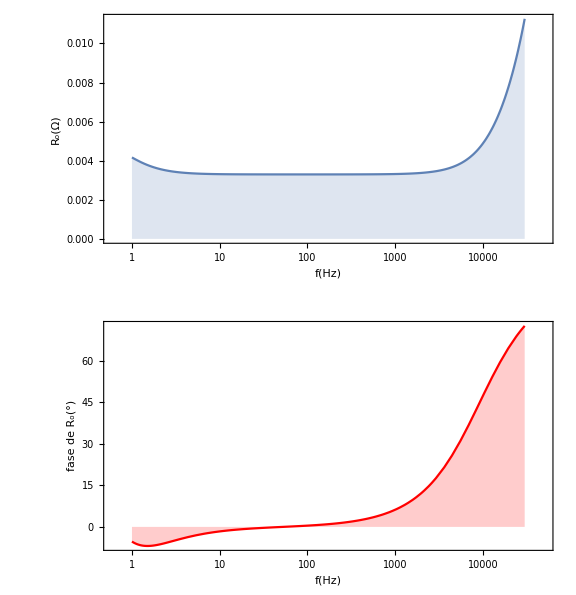

```mathematica
gr=GraphicsColumn[{
LogLinearPlot[Abs@r[f], {f, 1, 30000},Filling->0,PlotRange->{0, Full},PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,0}}, FrameLabel->{"f(Hz)","R_o(Ω)"}, AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}],
LogLinearPlot[(Arg@r[f])/Degree, {f, 1, 30000},Filling->0,PlotRange->Full,PlotTheme->"Detailed",PlotRangePadding->{{-1,-1},{0,0}}, PlotStyle->Red,FrameLabel->{"f(Hz)","fase de R_o("<>ToString[Degree, StandardForm]<>")"}, AspectRatio->0.5, PlotLegends->None, ImagePadding->{{60, 5}, {40, 5}}]
}, ImageSize->Large
]
```

```mathematica
TimeSeriesWindow[r,{1,30000}]//Mean/*Abs
```

0.00348364

```mathematica
TimeSeriesWindow[r,{1,30000}]//Mean@*Abs
```

0.0038601

```mathematica
TimeSeriesWindow[r,{1,30000}]//MinMax@*Arg/*(# /Degree&)
```

{-6.90256,72.201}

```mathematica
Export["../../../../informe/img/sim/R_out-zoom.pdf", gr];
```